```mathematica
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];
pirange = logspace[100, .01, 100];
```

```mathematica
pi0[dl_, kd_, c_]:= c * ( (dl/kd) / (1 + (dl/kd) ) )
```

```mathematica
factive[dl_, kd_, c_, pi1_, pi2_, n0_, n2_] =((pi2/(pi1+pi2))^n2)*((pi0[dl, kd, c]/(pi1+pi0[dl, kd, c]))^n0)
```

((c dl)/((1+dl/kd) kd ((c dl)/((1+dl/kd) kd)+pi1)))^n0 (pi2/(pi1+pi2))^n2

```mathematica
mfpts[dl_, kd_, c_, pi1_, pi2_, n0_, n2_] =n2*(1/(pi2+pi1))+n0*(1/(pi0[dl, kd, c]+pi1))
```

n0/((c dl)/((1+dl/kd) kd)+pi1)+n2/(pi1+pi2)

```mathematica
Manipulate[Plot[factive[dl, kd, c, pi1, pi2, n0, n2], {dl, 1, 4000}, PlotRange->{{0 ,4000}, {0, 1.5}}], {c, 0.01, 10}, {kd, 1, 100000}, {pi1, .01, 10}, {pi2, .01, 10},{n0, 5,5}, {n2, 5,5}]
```

```mathematica
Manipulate[Plot[mfpts[dl, kd, c, pi1, pi2, n0, n2], {dl, 1, 4000}, PlotRange->{{0 ,4000}, {0, 10}}], {c, 0.01, 10}, {kd, 1, 100000}, {pi1, .01, 10}, {pi2, .01, 10},{n0, 5,5}, {n2, 5,5}]
```

```mathematica
factivetable = Table[factive[dl, kd, c, pi1, pi2, n0, n2], {c, 0.01, 2, .1}, {kd, 1, 10000 ,1000}, {pi1, .01, 2, .1}, {pi2, .01, 2, .1},{n0, 5,5}, {n2, 5,5}, {dl, 1, 4000, 100}]
mfptstable = Table[mfpts[dl, kd, c, pi1, pi2, n0, n2], {c, 0.01, 2, .1}, {kd, 1, 10000 ,1000}, {pi1, .01, 2, .1}, {pi2, .01, 2, .1},{n0, 5,5}, {n2, 5,5}, {dl, 1, 4000, 100}]
```

{{1},18,{1}}
 |  |  |  |

```mathematica
threaded = RandomSample[Thread[{Flatten[factivetable],Flatten[mfptstable]}], 20000];
```

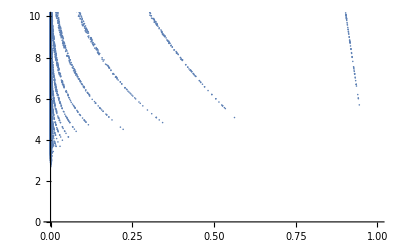

```mathematica
ListPlot[threaded, PlotRange->{{0 ,1}, {0, 10}}]
```

```mathematica
factive2[pi02_, pi1_, pi2_, n0_, n2_] =((pi2/(pi1+pi2))^n2)*((pi02/(pi1+pi02))^n0)
```

(pi02/(pi02+pi1))^n0 (pi2/(pi1+pi2))^n2

```mathematica
mfpts2[pi02_,pi1_, pi2_, n0_, n2_] =n2*(1/(pi2+pi1))+n0*(1/(pi0_2+pi1))
```

n2/(pi1+pi2)+n0/(pi1+2 pi0_)

```mathematica
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];
pirange = logspace[100, .01, 100];
```

```mathematica
factive2table = Table[factive2[pi02 ,pi1, pi2, n0, n2], {pi02, pirange}, {pi1, pirange}, {pi2, pirange},{n0, 5,5}, {n2, 5,5}];
mfpts2table = Table[mfpts2[pi02 ,pi1, pi2, n0, n2], {pi02, pirange}, {pi1, pirange}, {pi2, pirange},{n0, 5,5}, {n2, 5,5}];
```

```mathematica
threaded = RandomSample[Thread[{Flatten[factivetable],Flatten[mfptstable]}], 20000];
```

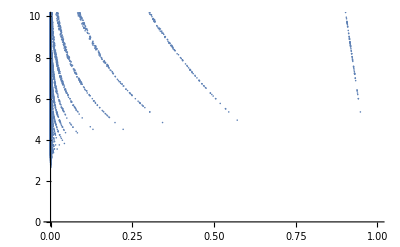

```mathematica
ListPlot[threaded, PlotRange->{{0 ,1}, {0, 10}}]
```